## Calculating the probability distribution of the focal trait effect size.

See Section S1.2 for derivation

```mathematica
S[n_,r_ ]:=(2 π^(n/2))/Gamma[n/2] r^(n-1)
```

```mathematica
P[a1_,n_,a_]:=S[n-1,√(a^2-a1^2)]/S[n,a] a/(√(a^2-a1^2))HeavisideTheta[a^2-a1^2]
Simplify[P[a1,n,a],Assumptions->a1>0&&a>a1]
```

(a^(2-n) (a^2-a1^2)^(1/2 (-3+n)) Gamma[n/2])/(√π Gamma[1/2 (-1+n)])

Figure 1b

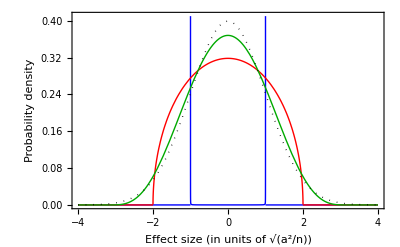

```mathematica
Plot[{1/(√1.0001)P[x/√1.0001,1.0001,1],1/(√4)P[x/√4,4,1],1/(√10)P[x/√10,10,1],1/(√(2π))Exp[-x^2/2]},{x,-4,4},MaxRecursion->15,PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Darker[Green]},{Thick,Black,Dotted}},Frame->True,BaseStyle->{FontSize->24},PlotRange->{{-4,4},{0,0.41}},FrameLabel->{"Effect size (in units of 
StyleBox[SqrtBox[
  RowBox[{SuperscriptBox[\"a\", \"2\"], \"/\", \"n\"}]],\nFontSize->14])","Probability density"},FrameTicks->{Automatic,Automatic,None,None},FrameTicksStyle->Directive[18],FrameStyle->Thickness[0.0025]]
```

## Calculating the first two moments of change in allele frequency.

We show here the two dimensional version of the formulae. The generalization to n dimensions is trivial.

```mathematica
W[r1_,r2_]:=Exp[-(r1^2+r2^2)/(2 w^2)];
f[r1_,r2_]:=1/(2π σ^2)Exp[-((r1+2q a1)^2+(r2+2q a2)^2)/(2 σ^2)];
W00=Integrate[f[r1,r2] W[r1,r2],{r1,-∞,∞},{r2,-∞,∞},Assumptions->w>0&&σ>0]//Simplify
W10=Integrate[f[r1,r2]W[r1+a1,r2+a2],{r1,-∞,∞},{r2,-∞,∞},Assumptions->w>0&&σ>0]//Simplify
W11=Integrate[f[r1,r2]W[r1+2a1,r2+2a2],{r1,-∞,∞},{r2,-∞,∞},Assumptions->w>0&&σ>0]//Simplify
```

(ⅇ^(-(2 (a1^2+a2^2) q^2)/(w^2+σ^2)) w^2)/(w^2+σ^2)

(ⅇ^(-((a1^2+a2^2) (1-2 q)^2)/(2 (w^2+σ^2))) w^2)/(w^2+σ^2)

(ⅇ^(-(2 (a1^2+a2^2) (-1+q)^2)/(w^2+σ^2)) w^2)/(w^2+σ^2)

There are n individuals in the population of the next generation. For each one of them the probabilities for the genotypes being 00,10,11 is p^2 W00,2pq W10,q^2 W11. Therefore, for each individual the mean and variance of the allele count is:

```mathematica
Ei=Series[(0(1-q)^2 W00+(1/2) 2q(1-q)W10+1 q^2 W11)/((1-q)^2 W00+ 2q(1-q)W10+ q^2 W11)/.(a1^2+a2^2)->a^2,{a,0,2}]//Simplify
Vi=Series[((0-q)^2(1-q)^2 W00+(1/2-q)^2 2q(1-q)W10+(1-q)^2 q^2 W11)/((1-q)^2 W00+2q(1-q)W10+q^2 W11)/.(a1^2+a2^2)->a^2,{a,0,1}]//Simplify
```

q-((q (1-3 q+2 q^2)) a^2)/(2 (w^2+σ^2))+O[a]^3

-1/2 (-1+q) q+O[a]^2

The overall change in frequency is and its variance are then

```mathematica
Edq=1/n∑_(i=1)^n Ei-q=-((q (1-3 q+2 q^2)) a^2)/(2(w^2+σ^2))=-(q (1-q)(1-2q) a^2)/(2(w^2+σ^2))=-a^2/(w^2+σ^2)q (1-q)(1/2-q) 
Vdq=V(1/n∑_(i=1)^n Ei-q)=1/n^2∑_(i=1)^n Vi=n(q(1-q))/(2 n^2)=(q(1-q))/(2n)
```

## Calculating the sojourn time. (Notation follows Ewens [2004])

```mathematica
m=-s/(2n) x (1-x)(1/2-x);
(*s here and throughout this notebook is the scaled selection coefficient. Lower case s is used to avoid confusion with the surface of the n-sphere defined above*)
v=(x(1-x))/(2n);
Ψ=Exp[-Integrate[2m/v,x]]
p1=Integrate[Ψ,{x,0,1/(2n)}]/Integrate[Ψ,{x,0,1}]//Simplify
p0=1-p1//Simplify
τ=Simplify[Piecewise[{{2 p0 1/(v Ψ)Integrate[Ψ,{x,0,y}]/.y->x,x≤ 1/(2 n)},{2 p1 1/(v Ψ)Integrate[Ψ,{x,y,1}]/.y->x,x>1/(2 n)}}],Assumptions->n>0&&s>0]
```

ⅇ^(10 x-10 x^2)

1/2 (1+Erf[√(5/2) (-1+1/n)]/Erf[√(5/2)])

1/2-Erf[√(5/2) (-1+1/n)]/(2 Erf[√(5/2)])

Piecewise[{{-(ⅇ^(5/2 (1-2 x)^2) n √((2 π)/5) (1/2-Erf[√(5/2) (-1+1/n)]/(2 Erf[√(5/2)])) (Erf[√(5/2)]+Erf[√(5/2) (-1+2 x)]))/((-1+x) x), 2 n x≤1}, {-(ⅇ^(5/2 (1-2 x)^2) n √(π/10) (1+Erf[√(5/2) (-1+1/n)]/Erf[√(5/2)]) (Erf[√(5/2)]-Erf[√(5/2) (-1+2 x)]))/((-1+x) x), 2 n x>1}, {0, True}}]

## Calculating summaries of the genetic architecture

```mathematica
t[x_,s_,n_]:=Piecewise[{{(ⅇ^(1/4 s (1-2 x)^2))/(x(1-x))(n √(π/s))/Erf[(√s)/2] Erf[1/2 (-1+1/n) √s,(√s)/2]Erf[-1/2 √s (-1+2 x),(√s)/2], 2 n x≤1}, {(ⅇ^(1/4 s (1-2 x)^2))/(x(1-x))(n √(π/s))/Erf[(√s)/2] Erf[-1/2 (-1+1/n) √s,(√s)/2] Erf[1/2 √s (-1+2 x),(√s)/2], 2 n x>1}, {0, True}}];
(*When evaluating expressions of the form Erf[x]-Erf[y] the use of Erf[y,x]=Erf[x]-Erf[y] provides better accuracy*)
P[a1_,n_,a_]:=(a^(2-n) (a^2-a1^2)^(1/2 (-3+n)) Gamma[n/2])/(√π Gamma[1/2 (-1+n)])HeavisideTheta[a^2-a1^2];
(*The HeavisideTheta allows us to define P[a1,n,a] for any value of a1 and thereby simplifies integration limits in the expressions below*)
```

The contribution to genetic variance (Fig. 2a)

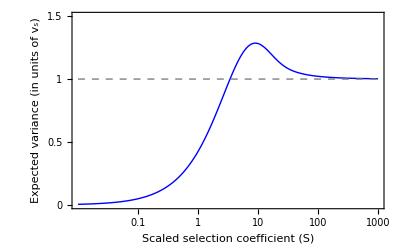

```mathematica
vtot[s_]:=NIntegrate[t[x,s,1000] s/2 x(1-x),{x,0,1}];
(* We measue v in units of Subscript[v, s], making E(Subscript[a, 1]^2|s)=s. In the above expression Subscript[a, 1] has been integrated out. See Eq. S24.*)
tbl=Table[{s,vtot[s]},{s,10^Range[-2,3,0.01]}];
ListLogLinearPlot[{tbl,{{0.01,1},{1000,1}}},Joined->True,PlotStyle->{{Thick,Blue},{Dashed,Gray},{Dashed,Red},{Dotted,Red}},Frame->True,BaseStyle->{FontSize->24},PlotRange->{{0.01,1000},{0,1.5}},FrameLabel->{"Scaled selection coefficient (S)","Expected variance\n(in units of v_s)"},FrameTicks->{{0.1,1,10,100,1000},{0,0.25,0.5,0.75,1,1.25,1.5},None,None},FrameTicksStyle->Directive[18],FrameStyle->Thickness[0.0025]]
```

The distribution of genetic variance by MAF (Fig. 2b)

```mathematica
F[xmin_,s_]:=NIntegrate[(t[x,s,10000]+t[1-x,s,10000]) s x (1-x),{x,xmin,0.5}];
lst1=Table[{x,100*F[x,1]/F[0,1]},{x,Range[0,0.5,0.001]}];
lst3=Table[{x,100*F[x,3]/F[0,3]},{x,Range[0,0.5,0.001]}];
lst10=Table[{x,100*F[x,10]/F[0,10]},{x,Range[0,0.5,0.001]}];
lst30=Table[{x,100*F[x,30]/F[0,30]},{x,Range[0,0.5,0.001]}];
lst100=Table[{x,100*F[x,100]/F[0,100]},{x,Range[0,0.5,0.001]}];
```

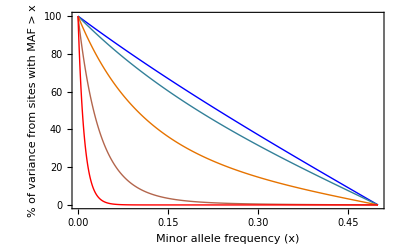

```mathematica
ListPlot[{lst1,lst3,lst10,lst30,lst100},Joined->True,PlotStyle->{{Thick,RGBColor[0,0,1]},{Thick,RGBColor[0.2,0.5,0.6]},{Thick,RGBColor[0.9,0.45,0]},{Thick,RGBColor[0.7,0.4,0.3]},{Thick,RGBColor[1,0,0]}},Frame->True,BaseStyle->{FontFamily->"Cambria",FontSize->20},PlotRange->{{0,0.5},{0,100}},FrameLabel->{"Minor allele frequency (x)","% of variance from sites\n with MAF > x"},FrameTicks->{Automatic,Automatic,None,None},FrameTicksStyle->Directive[18],FrameStyle->Thickness[0.0025]]
```

The density of loci with contribution to variance v (in units of v_s)

```mathematica
rho[v_,n_,s_]:=2NIntegrate[(t[1/2(1-√(1-2v/a1^2)),s,1000]+t[1/2(1+√(1-2v/a1^2)),s,1000])1/(2 a1^2)1/(√(1-2v/a1^2))1/(√n)P[a1/(√n),n,√(s/4)],{a1,√(2v),∞}]; (*Eq. S30*)
rho1D[v_,s_]:=(t[1/2(1-√(1-8v/s)),s,1000]+t[1/2(1+√(1-8v/s)),s,1000])2/s 1/(√(1-8v/s));
rhoHighPleiotropy[v_,s_]:=2NIntegrate[(t[1/2(1-√(1-2v/ a1^2)),s,1000]+t[1/2(1+√(1-2v/ a1^2)),s,1000])1/(2 a1^2)1/(√(1-2v/a1^2))1/(√(2π s/4))Exp[-4 a1^2/(2s)],{a1,√(2v),∞}];
```

The number of loci contributing more than v (per mutational input 2NU)

```mathematica
Fnum[v_,n_,s_]:= NIntegrate[rho[u,n,s],{u,v,∞}]; (*Eq. S31*)
Fnum1D[v_,s_]:= NIntegrate[rho1D[u,s],{u,v,∞}];
FnumvHighPleiotropy[v_,s_]:= NIntegrate[rhoHighPleiotropy[u,s],{u,v,∞}];
(*we overide this definition for a more computationaly efficient one:*) 
FnumvHighPleiotropy[v_,s_]:=2NIntegrate[(t[1/2(1-√(1-2u/ a1^2)),s,1000]+t[1/2(1+√(1-2u/ a1^2)),s,1000])1/(2 a1^2)1/(√(1-2u/a1^2))1/(√(2π s/4))Exp[-4 a1^2/(2s)],{u,v,∞},{a1,√(2u),∞}];
```

The cumulative contribution to variance from loci contributing more than v

```mathematica
Fv[v_,n_,s_]:=NIntegrate[rho[u,n,s]u,{u,v,∞}]; 
Fv1D[v_,s_]:=NIntegrate[rho1D[u,s]u,{u,v,∞}];
FvHighPleiotropy[v_,s_]:=NIntegrate[rhoHighPleiotropy[u,s]u,{u,v,∞}]; (*we overide this definition for a more computationaly efficient one:*)
FvHighPleiotropy[v_,s_]:=2NIntegrate[(t[1/2(1-√(1-2u/ a1^2)),s,1000]+t[1/2(1+√(1-2u/ a1^2)),s,1000])1/(2 a1^2)1/(√(1-2u/a1^2))1/(√(2π s/4))Exp[-4 a1^2/(2s)]u,{u,v,∞},{a1,√(2u),∞}];
```

% of contribution from loci contributing more than v

```mathematica
G[v_,n_,s_]:=Fv[v,n,s]/vtot[s]; (*Eq. S39*)
G1D[v_,s_]:=Fv1D[v,s]/vtot[s];
GHighPleiotropy[v_,s_]:=FvHighPleiotropy[v,s]/vtot[s];
```

These expressions would allow us to create Figs. 3 and 4. However, in order to effciently evaluate the high pleiotropy expressions we need to avoid the double integration. We therefore tabulate the one dimensional case and use it to calculate the high pleiotropy limit.

```mathematica
vrng=Range[0,30,0.1];
```

```mathematica
s=100
tbl=Table[{v,G1D[v,s]},{v,vrng}];
intrs1001D=Interpolation[tbl];
intr=Interpolation[tbl];
fHP[v_]:=Quiet[Chop[2NIntegrate[1/(√(2π))ⅇ^(-a^2/2)a^2 intr[v/a^2],{a,0,∞}]]];
tbl=Table[{v,fHP[v]},{v,vrng}];
intrs100HP=Interpolation[tbl];
tbl=Table[{v,Fnum1D[v,s]},{v,vrng}];
intrnums1001D=Interpolation[tbl];
intr=Interpolation[tbl];
fHP[v_]:=Quiet[Chop[2NIntegrate[1/(√(2π))ⅇ^(-a^2/2)intr[v/a^2],{a,0,∞}]]];
tbl=Table[{v,fHP[v]},{v,vrng}];
intrnums100HP=Interpolation[tbl];
```

```mathematica
s=30
tbl=Table[{v,G1D[v,s]},{v,vrng}];
intrs301D=Interpolation[tbl];
intr=Interpolation[tbl];
fHP[v_]:=Quiet[Chop[2NIntegrate[1/(√(2π))ⅇ^(-a^2/2)a^2 intr[v/a^2],{a,0,∞}]]];
tbl=Table[{v,fHP[v]},{v,vrng}];
intrs30HP=Interpolation[tbl];
tbl=Table[{v,Fnum1D[v,s]},{v,vrng}];
intrnums301D=Interpolation[tbl];
intr=Interpolation[tbl];
fHP[v_]:=Quiet[Chop[2NIntegrate[1/(√(2π))ⅇ^(-a^2/2)intr[v/a^2],{a,0,∞}]]];
tbl=Table[{v,fHP[v]},{v,vrng}];
intrnums30HP=Interpolation[tbl];
```

30

```mathematica
s=10
tbl=Table[{v,G1D[v,s]},{v,vrng}];
intrs101D=Interpolation[tbl];
intr=Interpolation[tbl];
fHP[v_]:=Quiet[Chop[2NIntegrate[1/(√(2π))ⅇ^(-a^2/2)a^2 intr[v/a^2],{a,0,∞}]]];
tbl=Table[{v,fHP[v]},{v,vrng}];
intrs10HP=Interpolation[tbl];
tbl=Table[{v,Fnum1D[v,s]},{v,vrng}];
intrnums101D=Interpolation[tbl];
intr=Interpolation[tbl];
fHP[v_]:=Quiet[Chop[2NIntegrate[1/(√(2π))ⅇ^(-a^2/2)intr[v/a^2],{a,0,∞}]]];
tbl=Table[{v,fHP[v]},{v,vrng}];
intrnums10HP=Interpolation[tbl];
```

10

```mathematica
vrng=Union[Range[0,0.99,0.01],Range[1,30,0.1]];(**small s require a tighter grid at low v**)
s=3
tbl=Table[{v,G1D[v,s]},{v,vrng}];
intrs31D=Interpolation[tbl];
intr=Interpolation[tbl];
fHP[v_]:=Quiet[Chop[2NIntegrate[1/(√(2π))ⅇ^(-a^2/2)a^2 intr[v/a^2],{a,0,∞}]]];
tbl=Table[{v,fHP[v]},{v,vrng}];
intrs3HP=Interpolation[tbl];
tbl=Table[{v,Fnum1D[v,s]},{v,vrng}];
intrnums31D=Interpolation[tbl];
intr=Interpolation[tbl];
fHP[v_]:=Quiet[Chop[2NIntegrate[1/(√(2π))ⅇ^(-a^2/2)intr[v/a^2],{a,0,∞}]]];
tbl=Table[{v,fHP[v]},{v,vrng}];
intrnums3HP=Interpolation[tbl];
```

3

```mathematica
vrng=Union[Range[0,0.99,0.01],Range[1,30,0.1]];(**small s require a tighter grid at low v**)
s=1
tbl=Table[{v,G1D[v,s]},{v,vrng}];
intrs11D=Interpolation[tbl];
intr=Interpolation[tbl];
fHP[v_]:=Quiet[Chop[2NIntegrate[1/(√(2π))ⅇ^(-a^2/2)a^2 intr[v/a^2],{a,0,∞}]]];
tbl=Table[{v,fHP[v]},{v,vrng}];
intrs1HP=Interpolation[tbl];
tbl=Table[{v,Fnum1D[v,s]},{v,vrng}];
intrnums11D=Interpolation[tbl];
intr=Interpolation[tbl];
fHP[v_]:=Quiet[Chop[2NIntegrate[1/(√(2π))ⅇ^(-a^2/2)intr[v/a^2],{a,0,∞}]]];
tbl=Table[{v,fHP[v]},{v,vrng}];
intrnums1HP=Interpolation[tbl];
```

1

```mathematica
(** Note: Some of the numerical intergrtions result in a small spurious imaginary part and therefore we use the Re[] function to remove it**)
```

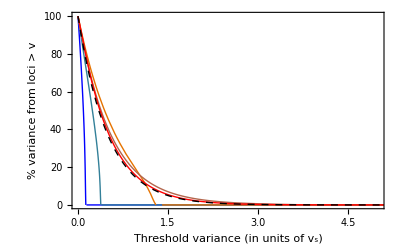

```mathematica
(**Fig 3a**)
Plot[{100*Re[intrs11D[v]],100*Re[intrs31D[v]],100*intrs101D[v],100*Re[intrs301D[v]],100*intrs1001D[v],100Exp[-2v]},{v,0,10},Frame->True,BaseStyle->{FontSize->20},PlotRange->{{0,5},{0,100}},PlotStyle->{{Thick,RGBColor[0,0,1]},{Thick,RGBColor[0.2,0.5,0.6]},{Thick,RGBColor[0.9,0.45,0]},{Thick,RGBColor[0.7,0.4,0.3]},{Thick,RGBColor[1,0,0]},{Black,Thick,Dashed}},FrameLabel->{"Threshold variance (in units of v_s)","% variance from loci > v"},FrameTicks->{Automatic,Automatic,None,None},FrameTicksStyle->Directive[18],FrameStyle->Thickness[0.0025]]
```

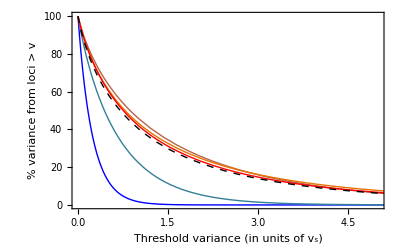

```mathematica
(**Fig 3b**)Plot[{100*Re[intrs1HP[v]],100*Re[intrs3HP[v]],100*intrs10HP[v],100*intrs30HP[v],100*intrs100HP[v],100Exp[-2 √v](1+2 √v)},{v,0,10},Frame->True,BaseStyle->{FontSize->20},PlotRange->{{0,5},{0,100}},PlotStyle->{{Thick,RGBColor[0,0,1]},{Thick,RGBColor[0.2,0.5,0.6]},{Thick,RGBColor[0.7,0.4,0.3]},{Thick,RGBColor[0.9,0.45,0]},{Thick,RGBColor[1,0,0]},{Black,Thick,Dashed}},FrameLabel->{"Threshold variance (in units of v_s)","% variance from loci > v"},FrameTicks->{Automatic,Automatic,None,None},FrameTicksStyle->Directive[18],FrameStyle->Thickness[0.0025]]
```

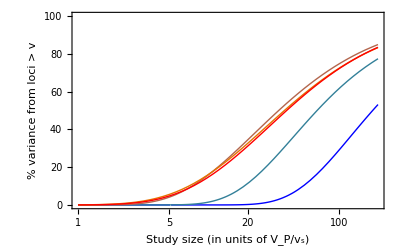

```mathematica
(**Fig 4a**)LogLinearPlot[{100*Re[intrs1HP[30/ns]],100*Re[intrs3HP[30/ns]],100*intrs10HP[30/ns],100*intrs30HP[30/ns],100*intrs100HP[30/ns]},{ns,1,200},Frame->True,BaseStyle->{FontSize->20},PlotRange->{{0,5},{0,100}},PlotStyle->{{Thick,RGBColor[0,0,1]},{Thick,RGBColor[0.2,0.5,0.6]},{Thick,RGBColor[0.7,0.4,0.3]},{Thick,RGBColor[0.9,0.45,0]},{Thick,RGBColor[1,0,0]},{Black,Dashed}},FrameLabel->{"Study size (in units of V_P/v_s)","% variance from loci > v"},FrameTicks->{Automatic,Automatic,None,None},FrameTicksStyle->Directive[18],FrameStyle->Thickness[0.0025]]
```

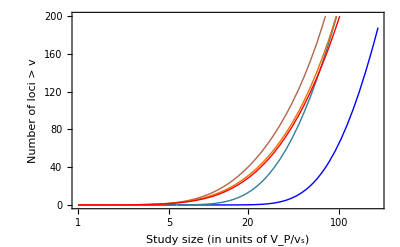

```mathematica
(**Fig 4b**)LogLinearPlot[{250*Re[intrnums1HP[30/ns]],250*Re[intrnums3HP[30/ns]],250*intrnums10HP[30/ns],250*intrnums30HP[30/ns],250*intrnums100HP[30/ns]},{ns,1,200},Frame->True,BaseStyle->{FontSize->20},PlotRange->{{0,5},{0,200}},PlotStyle->{{Thick,RGBColor[0,0,1]},{Thick,RGBColor[0.2,0.5,0.6]},{Thick,RGBColor[0.7,0.4,0.3]},{Thick,RGBColor[0.9,0.45,0]},{Thick,RGBColor[1,0,0]},{Black,Dashed}},FrameLabel->{"Study size (in units of V_P/v_s)","Number of loci > v"},FrameTicks->{Automatic,Automatic,None,None},FrameTicksStyle->Directive[18],FrameStyle->Thickness[0.0025]]
```

## Calculating the first two moments of change in allele frequency with a non-zero phenotypic mean

We show here the two dimensional version of the formulae. The generalization to n dimensions is trivial.

```mathematica
W[r1_,r2_]:=Exp[-(r1^2+r2^2)/(2 w^2)];
f[r1_,r2_]:=1/(2π σ^2)Exp[-((r1+2q a1-rbar1)^2+(r2+2q a2-rbar2)^2)/(2 σ^2)];
W00=Integrate[f[r1,r2]W[r1,r2],{r1,-∞,∞},{r2,-∞,∞},Assumptions->w>0&&σ>0]//Simplify
W10=Integrate[f[r1,r2]W[r1+a1,r2+a2],{r1,-∞,∞},{r2,-∞,∞},Assumptions->w>0&&σ>0]//Simplify
W11=Integrate[f[r1,r2]W[r1+2a1,r2+2a2],{r1,-∞,∞},{r2,-∞,∞},Assumptions->w>0&&σ>0]//Simplify
```

(ⅇ^(-(4 a1^2 q^2+4 a2^2 q^2-4 a1 q rbar1+rbar1^2-4 a2 q rbar2+rbar2^2)/(2 (w^2+σ^2))) w^2)/(w^2+σ^2)

(ⅇ^(-(a1^2 (1-2 q)^2+a2^2 (1-2 q)^2+a1 (2-4 q) rbar1+rbar1^2+a2 (2-4 q) rbar2+rbar2^2)/(2 (w^2+σ^2))) w^2)/(w^2+σ^2)

(ⅇ^(-(4 a1^2 (-1+q)^2+4 a2^2 (-1+q)^2-4 a1 (-1+q) rbar1+rbar1^2-4 a2 (-1+q) rbar2+rbar2^2)/(2 (w^2+σ^2))) w^2)/(w^2+σ^2)

There are n individuals in the population of the next generation. For each one of them the probabilities for the genotypes 00,10,11 is p^2 W00,2pq W10,q^2 W11. Therefore, for each individual the mean and variance of the allele count is:

```mathematica
Ei=Series[(0(1-q)^2 W00+(1/2) 2q(1-q)W10+1 q^2 W11)/((1-q)^2 W00+ 2q(1-q)W10+ q^2 W11)/.(w^2+σ^2)->1/x/.a1->a Cos[θ]/.a2->a Sin[θ],{x,0,1},{a,0,7}]/.x->1/(w^2+σ^2)//FullSimplify
Vi=Series[((0-q)^2(1-q)^2 W00+(1/2-q)^2 2q(1-q)W10+(1-q)^2 q^2 W11)/((1-q)^2 W00+2q(1-q)W10+q^2 W11)/.(w^2+σ^2)->1/x/.a1->a Cos[θ]/.a2->a Sin[θ],{x,0,1},{a,0,7}]/.x->1/(w^2+σ^2)//FullSimplify
```

SeriesData::sdatv: First argument 1/w^2 + σ^2 is not a valid variable.

q+((-1+q) q (rbar1 Cos[θ]+rbar2 Sin[θ]) a-1/2 ((-1+q) q (-1+2 q)) a^2+O[a]^8)/(w^2+σ^2)+O[1/(w^2+σ^2)]^2

SeriesData::sdatv: First argument 1/w^2 + σ^2 is not a valid variable.

-1/2 (-1+q) q+1/(w^2+σ^2)(-1/2 ((-1+q) q (-1+2 q) (rbar1 Cos[θ]+rbar2 Sin[θ])) a+1/4 (-1+q) q (1+2 (-1+q) q) a^2+O[a]^8)+O[1/(w^2+σ^2)]^2

The overall change in frequency is and its variance are then

```mathematica
Edq=1/n∑_(i=1)^n Ei-q=-((q (1-3 q+2 q^2)) a^2)/(8(w^2+σ^2))=-(q (1-q)(1-2q) a^2)/(8(w^2+σ^2))=-(rbar·a)/(w^2+σ^2) q(1-q) -a^2/(w^2+σ^2)q (1-q)(1/2-q) 
Vdq=V(1/n∑_(i=1)^n Ei-q)=1/(4 n^2)∑_(i=1)^n Vi=n(q(1-q))/(2 n^2)=(q(1-q))/(2n)
```